[Requires code for Figure 1c  from main file.]

### Jackdaws

Based on the median of the jackdaw data from Ling et al. (2019):

```mathematica
CVindMOB =0.270;
CVindTRANS =0.221;
CVherdMOB =0.551;
CVherdTRANS = 0.560;
CVratioMOB=0.497;
CVratioTRANS=0.393;
```

The decision tree is consistent with mobbing being more symmetric, while transiting birds exhibit more of an even split.

#### Herd-level only

[This is not that insightful, because the individual-level CV changes more dramatically with mobbing. See next section.]

Using only the population-level CV with an even split (f=1/2), the data are consistent with splits:

```mathematica
CVherdCs=Sqrt[(16 ⅇ^(Subscript[c, S]^2/4) (4+f Subscript[c, S]^2))/(π (4 ⅇ^(Subscript[c, S]^2/8) (1-f)+(4+Subscript[c, S]^2)f BesselI[0,Subscript[c, S]^2/8]+f Subscript[c, S]^2 BesselI[1,Subscript[c, S]^2/8])^2)-1];
```

with an average distance relative to σ [c_S=c/σ] for mobbing jackdaws of:

```mathematica
NSolve[(CVherdCs/.f->1/2)==CVherdMOB,Subscript[c, S]]
```

{{Reduce`ReduceVar[1]→3.51166}}

which is less than that observed for transitting jackdaws:

```mathematica
NSolve[(CVherdCs/.f->1/2)==CVherdTRANS,Subscript[c, S]]
```

{{Reduce`ReduceVar[1]→3.83952}}

Alternatively, if we estimated the degree of elongation, assuming a single patch [α = σy/σx]:

```mathematica
CVherdALT=Sqrt[(π (1+α^2))/(2  EllipticE[1-α^2]^2)-1];
```

Mobbing jackdaws are slightly

```mathematica
NSolve[CVherdALT==CVherdMOB,α]
```

{{α→0.636494}}

```mathematica
NSolve[CVherdALT==CVherdTRANS,α]
```

{{α→0.590317}}

#### Comparing to individual and herd level data (Panel 1C: Even herd split)

```mathematica
xTRANS=x/.Flatten[Solve[(tryV x)/(1-x)==3.2,x]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.444444

```mathematica
xMOB=x/.Flatten[Solve[(tryV x)/(1-x)==0.5,x]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.111111

```mathematica
CVherdC
```

√(-1+(16 ⅇ^(c_S^2/4) (4+f c_S^2))/(π (4 ⅇ^(c_S^2/8) (1-f)+f BesselI[1,c_S^2/8] c_S^2+f BesselI[0,c_S^2/8] (4+c_S^2))^2))

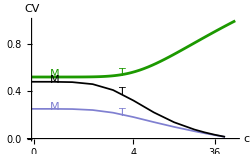

```mathematica
Show[
Plot[CVherdC/.σ->tryσ/.f->tryf/.c->(tryV x)/(1-x),{x,0,maxc},WorkingPrecision->50,PlotStyle->RGBColor[0.11,0.6,0.],PlotRange->All],
ListPlot[intplottingindC,Joined->True,PlotStyle->{Thickness[0.005],RGBColor[0.5,0.5,0.82]}],
ListPlot[Table[{intplottingindC[[i,1]],intplottingindC[[i,2]]/N[(CVherdC/.σ->tryσ/.f->tryf/.c->(tryV x)/(1-x)/.x->tab[[i]]),20]},{i,1,Length[forplottingindC]}],Joined->True,PlotStyle->{Thickness[0.005],Black}],

Graphics[Text[Style["T",RGBColor[0.5,0.5,0.82]],{xTRANS,CVindTRANS}]],
Graphics[Text[Style["T",RGBColor[0.11,0.6,0.]],{xTRANS,CVherdTRANS}]],
Graphics[Text[Style["T",Black],{xTRANS,CVratioTRANS}]],

Graphics[Text[Style["M",RGBColor[0.5,0.5,0.82]],{xMOB,CVindMOB}]],
Graphics[Text[Style["M",RGBColor[0.11,0.6,0.]],{xMOB,CVherdMOB}]],
Graphics[Text[Style["M",Black],{xMOB,CVratioMOB}]],

(*
Plot[CVindMOB,{x,0,maxc},PlotStyle->Black],
Plot[CVherdMOB,{x,0,maxc},PlotStyle->Black],
Plot[CVratioMOB,{x,0,maxc},PlotStyle->Black],

Plot[CVindTRANS,{x,0,maxc},PlotStyle->Black],
Plot[CVherdTRANS,{x,0,maxc},PlotStyle->Black],
Plot[CVratioTRANS,{x,0,maxc},PlotStyle->Black],
*)
AxesOrigin->{0,0},
PlotRange->{{0,maxc},{0,1}},Ticks->{xticks,Automatic},ImageSize->250,AxesLabel->{"c","CV"}
]
```